```mathematica
ClearAll["Global`*"]
```

{{0.785398,0.139},{2.2698,0.29},{6.51441,0.678}}

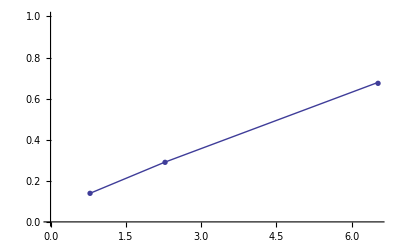

```mathematica
r={1/2,1.7/2,2.88/2};
F=r^2 π;
n={0.235,0.386,0.774}-0.096;
data=Table[{F[[i]],n[[i]]},{i,1,3}]//N
ListPlot[data,PlotRange->{0,1},Joined->True,PlotMarkers->{Automatic,7}]
```

```mathematica
lm=LinearModelFit[data,x,x]
lm["ParameterTable"]
```

FittedModel[0.0707719+0.0934923 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0707719 | 0.00850674 | 8.3195 | 0.076156
x | 0.0934923 | 0.00212213 | 44.0559 | 0.0144478

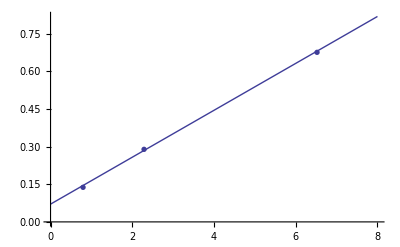

```mathematica
Show[Plot[Normal[lm],{x,0,8}],ListPlot[data,PlotRange->{0,1},PlotMarkers->{Automatic,7}]]
```

```mathematica
Rρ=4.026*10^-3;
Na=6.022*10^23;
hrel=0.1487;
M=348.72;
c=0.09349;

T=Log[2]/2*(Rρ*Na*hrel)/(c M)*1/(60*60*24*365)
sc=0.002;
sT=sc/c*T
sT/T
```

1.21527×10^11

2.59978×10^9

0.0213927